```mathematica
SetDirectory["~/worker/membrain/framefilter"];
Needs["PlotLegends`"]
```

```mathematica
fx[x_,y_]:=-hpp*Exp[-(x-xcpp)^2/(2w1pp)]*Exp[-(y-ycpp)^2/(2w2pp)]
```

```mathematica
curvfx[x_,y_]:=((1+D[fx[x,y],{x,1}]^2)D[fx[x,y],{y,2}]+(1+D[fx[x,y],{y,1}]^2)D[fx[x,y],{x,2}]-2*D[fx[x,y],{x,1}]*D[fx[x,y],{y,1}]*D[fx[x,y],{x,1},{y,1}])/(1+(D[fx[x,y],{x,1}])^2+(D[fx[x,y],{y,1}])^2)^(3/2)
```

```mathematica
curvfxg[x_,y_]:=((D[fx[x,y],{x,2}])*(D[fx[x,y],{y,2}])-(D[fx[x,y],{x,1},{y,1}])^2)/(1+(D[fx[x,y],{x,1}])^2+(D[fx[x,y],{y,1}])^2)^2
```

# Analysis

## Analyze, Antiparallel

```mathematica
<<"./dump.mx"
```

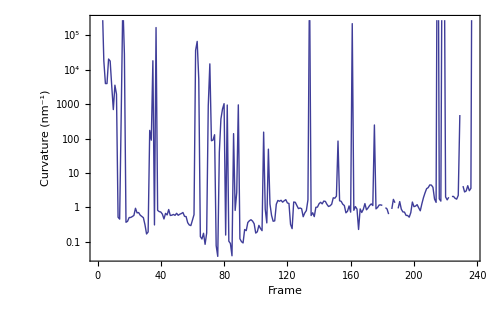

```mathematica
ListLogPlot[curves,PlotRange->All,Joined->True,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Unfiltered Curvature",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

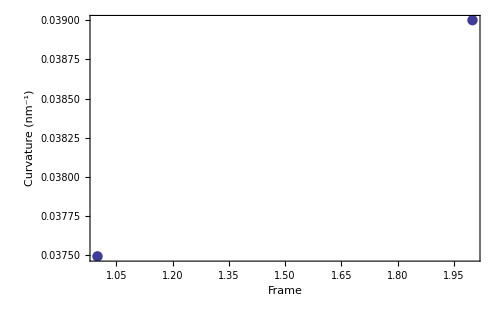

```mathematica
validinds=Position[Table[If[curves[[i]]≤0.06&&curves[[i]]≥0.006,1,0],{i,1,Length[curves]}],1];
curvesv=Table[curves[[validinds[[i,1]]]],{i,1,Length[validinds]}];
ListPlot[curvesv,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Filtered Curvature",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

```mathematica
Print["Arithmetic Mean Curvature, Geometric Mean Curvature"];
{1/Mean[curvesv],Mean[Table[1/curvesv[[i]],{i,1,Length[curvesv]}]]}
```

Arithmetic Mean Curvature, Geometric Mean Curvature

{26.1458,26.156}

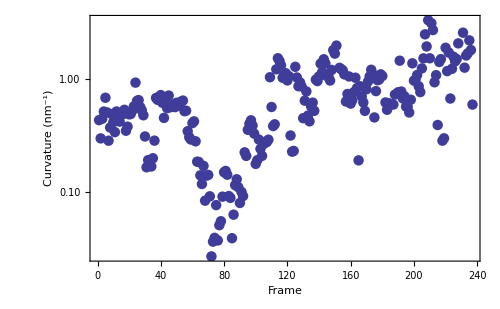

```mathematica
ListLogPlot[curves2,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Maximum Global Curvature",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

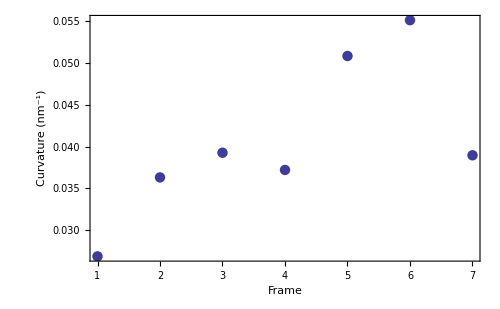

```mathematica
validinds2=Position[Table[If[curves2[[i]]≤0.06&&curves2[[i]]≥0.00001,1,0],{i,1,Length[curves2]}],1];
curvesv2=Table[curves2[[validinds2[[i,1]]]],{i,1,Length[validinds2]}];
ListPlot[curvesv2,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Maximum Local Curvature",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

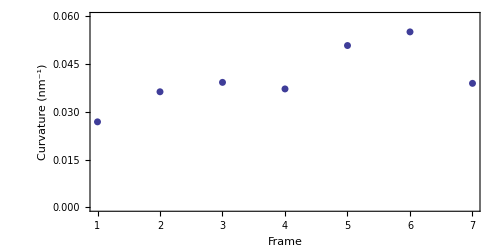

```mathematica
antitraj=ListPlot[curvesv2,PlotRange->{0,0.06},ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.01]}},FrameLabel->{"Frame","Curvature (nm^-1)","Antiparallel",""},BaseStyle->{14,FontFamily->"Helvetica",Bold},AspectRatio->1/2]
```

```mathematica
Print["Arithmetic Mean Curvature, Geometric Mean Curvature"];
{1/Mean[curvesv2],Mean[Table[1/curvesv2[[i]],{i,1,Length[curvesv]}]]}
```

Arithmetic Mean Curvature, Geometric Mean Curvature

{24.6004,32.3787}

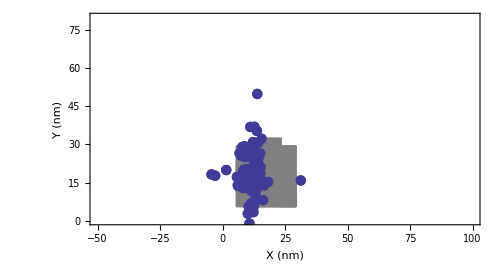

```mathematica
postraj=Table[{params[[i,4]]+shifter[[1]],params[[i,5]]+shifter[[2]]},{i,1,Length[params]}];
lptraj=ListPlot[postraj,Frame->True,ClippingStyle->Opacity[1],PlotStyle->{{PointSize[0.015]}},FrameLabel->{"X (nm)","Y (nm)","Antiparallel",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}];
plotregions=Show[Table[regions[[i]],{i,1,Length[regions],100}]];
Show[lptraj,plotregions,lptraj,AspectRatio->Automatic,ImageSize->500,PlotRange->{{-50,100},{0,80}},Axes->False]
```

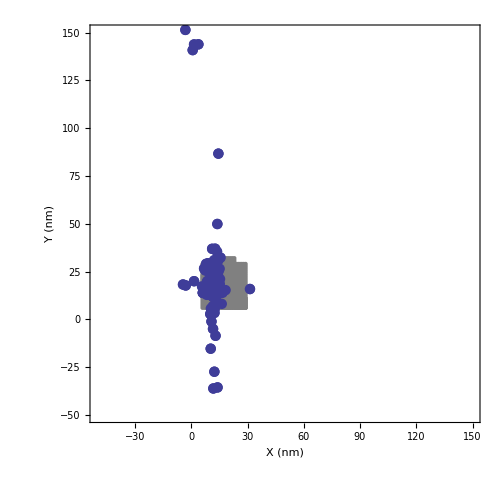

```mathematica
antimap=Show[lptraj,plotregions,lptraj,AspectRatio->Automatic,ImageSize->500,PlotRange->{{-50,150},{-50,150}},Axes->False]
```

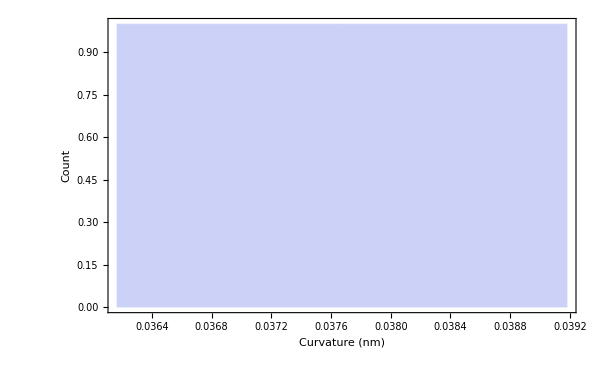

```mathematica
Histogram[curvesv,20,Frame->True,ImageSize->600,FrameLabel->{"Curvature (nm)","Count","Mean Curvature",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

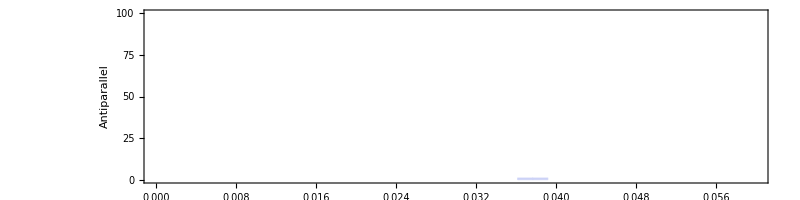

```mathematica
hanti=Histogram[curvesv,20,Frame->True,ImageSize->800,PlotRange->{{0,0.06},{0,100}},AspectRatio->1/4,FrameLabel->{"","Antiparallel","",""},BaseStyle->{14,FontFamily->"Helvetica",Bold},Axes->False]
```

```mathematica
minw=Table[If[params[[validinds[[i,1]],1]]≤params[[validinds[[i,1]],2]],params[[validinds[[i,1]],1]],params[[validinds[[i,1]],2]]],{i,1,Length[validinds]}];
maxw=Table[If[params[[validinds[[i,1]],1]]≥params[[validinds[[i,1]],2]],params[[validinds[[i,1]],1]],params[[validinds[[i,1]],2]]],{i,1,Length[validinds]}];
ratios=Table[maxw[[i]]/minw[[i]],{i,1,Length[maxw]}];
maxw2={};
For[i=1,i≤Length[maxw],i++,{
If[maxw[[i]]≤10^6,AppendTo[maxw2,maxw[[i]]]];
}];
minw2={};
For[i=1,i≤Length[minw],i++,{
If[minw[[i]]≤10^6,AppendTo[minw2,minw[[i]]]];
}];
```

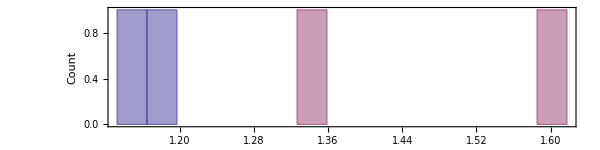

```mathematica
Histogram[{Log[10,Sqrt[minw2]],Log[10,Sqrt[maxw2]]},40,Frame->True,ImageSize->600,AspectRatio->1/4,FrameLabel->{"Log Witdh (nm)","Count","Log Gaussian Widths",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

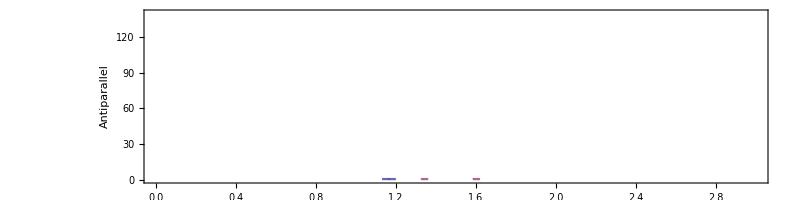

```mathematica
widanti=Histogram[{Log[10,Sqrt[minw2]],Log[10,Sqrt[maxw2]]},40,AspectRatio->1/4,ImageSize->800,Frame->True,PlotRange->{{0,3},{0,140}},BaseStyle->{14,FontFamily->"Helvetica",Bold},Axes->False,Frame->True,FrameLabel->{"","Antiparallel","",""}]
```

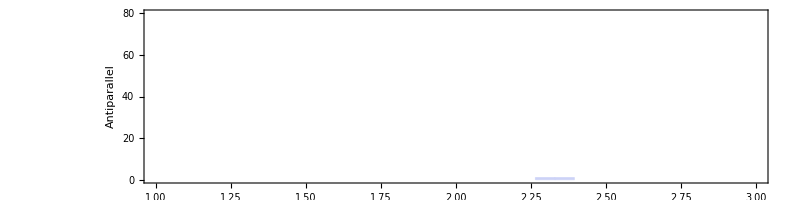

```mathematica
shortwidanti=Histogram[Log[10,minw2],40,AspectRatio->1/4,ImageSize->800,Frame->True,PlotRange->{{1,3},{0,80}},BaseStyle->{14,FontFamily->"Helvetica",Bold},Axes->False,Frame->True,FrameLabel->{"","Antiparallel","",""}]
```

```mathematica
{Mean[minw2],Mean[maxw2],Mean[maxw2]/Mean[minw2]}
```

{228.405,1079.66,4.72697}

```mathematica
Print["Arithmetic Mean Curvature, Geometric Mean Curvature"];
{1/Mean[curvesv2],Mean[Table[1/curvesv2[[i]],{i,1,Length[curvesv]}]]}
```

Arithmetic Mean Curvature, Geometric Mean Curvature

{24.6004,32.3787}

```mathematica
antishape={1/Mean[curvesv2],Sqrt[Mean[minw2]],Sqrt[Mean[maxw2]]}
```

{24.6004,15.1131,32.8583}

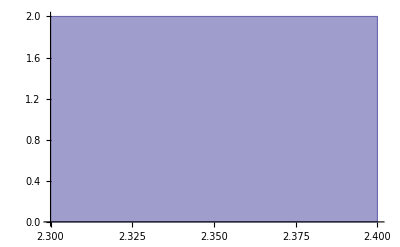

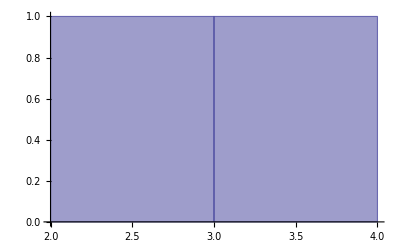

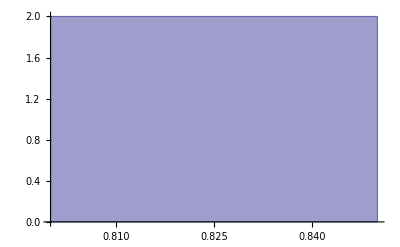

```mathematica
Histogram[{Log[10,Table[params[[validinds[[i,1]],1]],{i,1,Length[validinds]}]]}]
Histogram[{Log[10,Table[params[[validinds[[i,1]],2]],{i,1,Length[validinds]}]]}]
Histogram[{Log[10,Table[params[[validinds[[i,1]],3]],{i,1,Length[validinds]}]]}]
```

```mathematica
Mean[params]
```

{42971.9,1.79622×10^6,1.77727×10^11,12.5684,260.77}

```mathematica
wp1={};
wp2={};
hp1={};
unfilt=Table[params[[validinds[[i,1]]]],{i,1,Length[validinds]}];
For[i=1,i≤Length[unfilt],i++,{
If[unfilt[[i,1]]≤10^4,AppendTo[wp1,unfilt[[i,1]]]];
If[unfilt[[i,2]]≤10^2.8,AppendTo[wp2,unfilt[[i,2]]]];
If[unfilt[[i,3]]≤10^0.6,AppendTo[hp1,unfilt[[i,3]]]];
}];
```

```mathematica
{Mean[hp1],Mean[wp1],Mean[wp2]}
```

{Mean[{}],228.405,522.129}

```mathematica
curvfxs[x_,y_]=curvfx[x,y]/.{hpp->Mean[hp1],xcpp->0,ycpp->0,w1pp->Mean[wp1],w2pp->Mean[wp2]};
{Mean[hp1],Mean[wp1],Mean[wp2]}
```

{Mean[{}],228.405,522.129}

```mathematica
{a1,b1}={a,b}/.Solve[{Pi*a*b==67^2,a/b==antishape[[3]]/antishape[[2]]},{a,b}][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{55.7372,25.6362}

```mathematica
antione=NIntegrate[curvfxs[x,y],{x,-a1,a1},{y,-b1,b1}]
```

NIntegrate::inumr: The integrand 1.40625×10^-10\ ⅇ^-0.00656727\ x^2 - 0.00287285\ y^2\ x^2\ y^2\ Mean[{}]^3 + « 1 » + (0.00437818\ ⅇ^Times[« 2 »] + Times[« 2 »] - 0.0000191684\ ⅇ^Times[« 2 »] + « 1 »\ x^2)\ Mean[{}]\ (1 + « 1 »)/(1 + 0.0000191684\ « 2 »\ « 1 »^2 + 3.66812×10^-6\ ⅇ^-0.00437818\ « 1 » - « 1 »\ y^2\ Mean[{}]^2)^3/2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 55.7372}, {0, 25.6362}}.

NIntegrate[curvfxs[x,y],{x,-a1,a1},{y,-b1,b1}]

```mathematica
antione2=NIntegrate[curvfxs[x,y]^2,{x,-a1,a1},{y,-b1,b1}]
```

0.121371

```mathematica
curvfxs[x_,y_]=curvfx[x,y]/.{hpp->Mean[curvesv2],xcpp->0,ycpp->0,w1pp->Mean[wp1],w2pp->Mean[wp2]};
antione3=NIntegrate[curvfxs[x,y],{x,-a1,a1},{y,-b1,b1}]
```

0.0874072

```mathematica
antione4=NIntegrate[curvfxs[x,y],{x,-antishape[[3]],antishape[[3]]},{y,-antishape[[2]],antishape[[2]]}]
```

0.135104

```mathematica
Plot3D[curvfxs[x,y],{x,-a1,a1},{y,-b1,b1},PlotRange->All]
```

Plot3D::exclul: {Im[0.0000191684\ ⅇ^Times[« 2 »] + Times[« 2 »]\ x^2\ Mean[{}]^2 + 3.66812×10^-6\ ⅇ^Times[« 2 »] + Times[« 2 »]\ y^2\ Mean[{}]^2] - 0} must be a list of equalities or real-valued functions.

-Graphics3D-

# Residuals

## Antiparallel Residuals

```mathematica
<<"./antiparallel/framefilter/dump.mx"
```

```mathematica
validinds=Position[Table[If[curves[[i]]≤0.06&&curves[[i]]≥0.006,1,0],{i,1,Length[curves]}],1];
```

```mathematica
Dynamic[j]
resids={};
For[j=1,j≤Length[validinds],j++,{
w1p=params[[validinds[[j,1]],1]];
w2p=params[[validinds[[j,1]],2]];
hp=params[[validinds[[j,1]],3]];
xcp=params[[validinds[[j,1]],4]];
ycp=params[[validinds[[j,1]],5]];
curvfx2[x_,y_]=curvfx2[x,y]/.{hpp->hp,xcpp->xcp,ycpp->ycp,w1pp->w1p,w2pp->w2p};
resid=Sum[Abs[curvfx2[dats[[validinds[[j,1]],k,1]],dats[[validinds[[j,1]],k,2]]]-dats[[validinds[[j,1]],k,3]]],{k,1,Length[dats[[validinds[[j,1]]]]]}]/Length[dats[[validinds[[j,1]]]]];
AppendTo[resids,resid];
}];
```

```mathematica
antiresids=resids;
```

```mathematica
Mean[resids]
```

0.697584

# Gaussian Curvature

```mathematica
(*DumpSave["meta-analysos.mx","Global`"];*)
```

```mathematica
(*DumpSave["gaussian-curv.mx","Global`"];*)
```

## Antiparallel Gaussian Curvature

```mathematica
<<"./antiparallel/framefilter/dump.mx"
```

```mathematica
validinds=Position[Table[If[curves[[i]]≤0.06&&curves[[i]]≥0.006,1,0],{i,1,Length[curves]}],1];
```

```mathematica
Dynamic[j]
gausscurv={};
```

```mathematica
For[j=1,j≤Length[validinds],j++,{
w1p=params[[validinds[[j,1]],1]];
w2p=params[[validinds[[j,1]],2]];
hp=params[[validinds[[j,1]],3]];
xcp=params[[validinds[[j,1]],4]];
ycp=params[[validinds[[j,1]],5]];
curvfx2g[x_,y_]=curvfxg[x,y]/.{hpp->hp,xcpp->xcp,ycpp->ycp,w1pp->w1p,w2pp->w2p};
AppendTo[gausscurv,Table[curvfx2g[dats[[validinds[[j,1]],k,1]],dats[[validinds[[j,1]],k,2]]],{k,1,Length[dats[[validinds[[j,1]]]]]}]];
}];
```

```mathematica
kantivals=gausscurv;
```

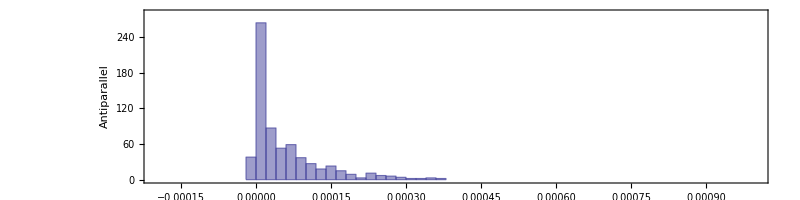

```mathematica
kanti=Histogram[{Table[Max[kantivals[[i]]],{i,1,Length[kantivals]}]},20,Frame->True,ImageSize->800,PlotRange->{{-0.0002,0.001},{0,280}},AspectRatio->1/4,FrameLabel->{"","Antiparallel","",""},BaseStyle->{14,FontFamily->"Helvetica",Bold},Axes->False]
```

# Curvature Integral Code

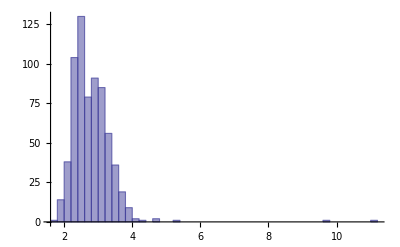

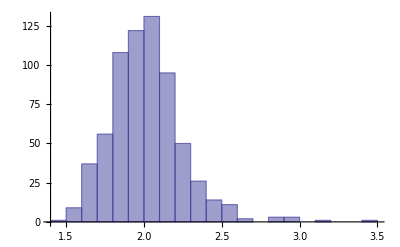

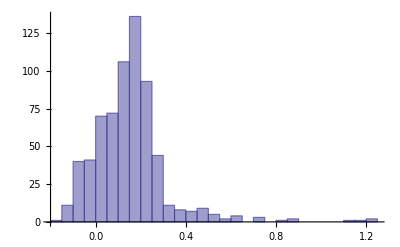

```mathematica
Histogram[{Log[10,Table[params[[validinds[[i,1]],1]],{i,1,Length[validinds]}]]}]
Histogram[{Log[10,Table[params[[validinds[[i,1]],2]],{i,1,Length[validinds]}]]}]
Histogram[{Log[10,Table[params[[validinds[[i,1]],3]],{i,1,Length[validinds]}]]}]
```

```mathematica
Mean[params]
```

{1.6211×10^8,143.319,1.95955×10^9,331.597,2.34392}

```mathematica
curvfx[x_,y_]:=((1+D[fx[x,y],{x,1}]^2)D[fx[x,y],{y,2}]+(1+D[fx[x,y],{y,1}]^2)D[fx[x,y],{x,2}]-2*D[fx[x,y],{x,1}]*D[fx[x,y],{y,1}]*D[fx[x,y],{x,1},{y,1}])/(1+(D[fx[x,y],{x,1}])^2+(D[fx[x,y],{y,1}])^2)^(3/2)
```

```mathematica
wp1={};
wp2={};
hp1={};
unfilt=Table[params[[validinds[[i,1]]]],{i,1,Length[validinds]}];
For[i=1,i≤Length[unfilt],i++,{
If[unfilt[[i,1]]≤10^4,AppendTo[wp1,unfilt[[i,1]]]];
If[unfilt[[i,2]]≤10^2.8,AppendTo[wp2,unfilt[[i,2]]]];
If[unfilt[[i,3]]≤10^2,AppendTo[hp1,unfilt[[i,3]]]];
}];
```

```mathematica
NIntegrate[curvfx[x,y]/.{hpp->Mean[hvals],xcpp->0,ycpp->0,w1pp->Mean[wp1],w2pp->Mean[wp2]},{x,-antishape[[2]],antishape[[2]]},{y,-antishape[[3]],antishape[[3]]}]
```

30.5259

# Gaussian Curvature

```mathematica
(*DumpSave["meta-analysos.mx","Global`"];*)
```

```mathematica
(*DumpSave["gaussian-curv.mx","Global`"];*)
```

## Antiparallel Gaussian Curvature

```mathematica
<<"./antiparallel/framefilter/dump.mx"
```

```mathematica
validinds=Position[Table[If[curves[[i]]≤0.06&&curves[[i]]≥0.006,1,0],{i,1,Length[curves]}],1];
```

```mathematica
Dynamic[j]
gausscurv={};
```

```mathematica
For[j=1,j≤Length[validinds],j++,{
w1p=params[[validinds[[j,1]],1]];
w2p=params[[validinds[[j,1]],2]];
hp=params[[validinds[[j,1]],3]];
xcp=params[[validinds[[j,1]],4]];
ycp=params[[validinds[[j,1]],5]];
curvfx2g[x_,y_]=curvfxg[x,y]/.{hpp->hp,xcpp->xcp,ycpp->ycp,w1pp->w1p,w2pp->w2p};
AppendTo[gausscurv,Table[curvfx2g[dats[[validinds[[j,1]],k,1]],dats[[validinds[[j,1]],k,2]]],{k,1,Length[dats[[validinds[[j,1]]]]]}]];
}];
```

```mathematica
kantivals=gausscurv;
```

```mathematica
kanti=Histogram[{Table[Max[kantivals[[i]]],{i,1,Length[kantivals]}]},18,Frame->True,ImageSize->800,PlotRange->{{-0.0002,0.001},{0,280}},AspectRatio->1/4,FrameLabel->{"","Antiparallel","",""},BaseStyle->{14,FontFamily->"Helvetica",Bold},Axes->False]
```

-Graphics-